# NG^21 P_04. Метод k-средних и RBF-сети

## 1. Обучающий и тестирующий наборы

```mathematica
Dimensions[data=Import["C:\\NG\\NG21P04Problem.xlsx",{"Sheets","БельскаяЕ"}]]
```

{3000,3}

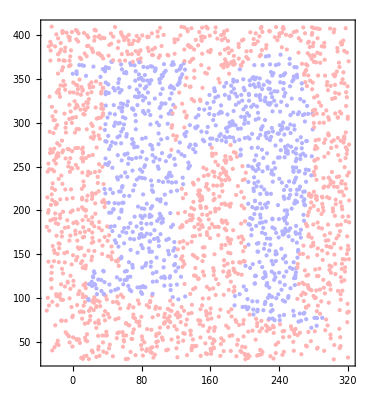

```mathematica
Fig0=Graphics[{{#3/.{1.->Hue[.67,.3,1],-1.->Hue[.00,.3,1]}, Point@{#1,#2}}&@@@Train}, Frame->True]
```

Фунцкия разделения исходного набора на 2 части

```mathematica
kmSplit[data_]:=Partition[RandomSample@data, UpTo[0.8Length@data]]
```

```mathematica
Map[Dimensions,{Train,Test}=kmSplit[data]]
```

{{2400,3},{600,3}}

Получение позиций синих и красных точек

```mathematica
Map[Dimensions,{blPoints=First[#]&/@Position[Train,1.],
rPoints=First[#]&/@Position[Train, -1.]}]
```

{{949},{1451}}

## 2. Метод k - средних

Центры кластеров, выбранных произвольным образом

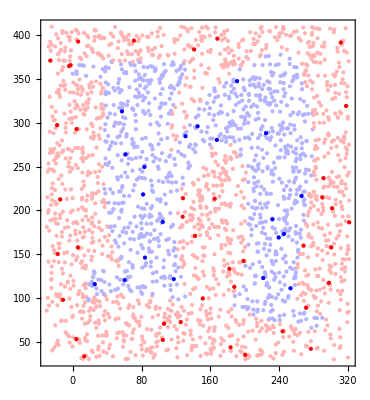

```mathematica
centB=Take[RandomSample[Train⟦blPoints,1;;2⟧],UpTo[20]];
centR=Take[RandomSample[Train⟦rPoints,1;;2⟧],UpTo[40]];
Show[Fig0, Graphics[{PointSize@Medium,Red, Point@centR, Blue, Point@centB}]]
```

Пустые кластеры

```mathematica
CB=ConstantArray[{},20];
CR=ConstantArray[{},40];
```

```mathematica
First@RandomChoice[blPoints,1]
Train[[%, 1;;2]]
First@Nearest[centB->"Index", %,1]
AppendTo[CB⟦%⟧,%%%]
```

```mathematica
AppendTo[CB⟦First@Nearest[centB->"Index", Train[[#, 1;;2]],1]⟧,#]&@First@RandomChoice[blPoints,1]
```

{317}

Сортировка точек по кластерам и нахождение новых центров

```mathematica
centB0={};
```

```mathematica
Do[AppendTo[CB⟦First@Nearest[centB->"Index", Train[[p, 1;;2]],1]⟧,p],{p, blPoints}];
```

```mathematica
While[centB0≠centB,
centB0=centB;
centB=Mean[Train⟦CB⟦#⟧,1;;2⟧]&/@Range[20];
CB=ConstantArray[{},20];
Do[AppendTo[CB⟦First@Nearest[centB->"Index", Train[[p, 1;;2]],1]⟧,p],{p, blPoints}];
]
```

```mathematica
centB
```

{{236.124,183.175},{29.8463,118.342},{97.5784,186.573},{260.895,231.674},{102.863,341.15},{59.046,279.555},{255.062,85.6358},{51.7744,342.597},{248.034,290.686},{110.271,129.36},{137.356,283.92},{67.2141,167.904},{236.695,138.659},{234.842,348.14},{56.7336,216.619},{102.58,241.937},{185.955,312.721},{69.8098,120.352},{217.561,243.325},{212.744,103.676}}

```mathematica
centR0={};
```

```mathematica
Do[AppendTo[CR⟦First@Nearest[centR->"Index", Train[[p, 1;;2]],1]⟧,p],{p, rPoints}]
```

```mathematica
While[centR0≠centR,
centR0=centR;
centR=Mean[Train⟦CR⟦#⟧,1;;2⟧]&/@Range[40];
CR=ConstantArray[{},40];
Do[AppendTo[CR⟦First@Nearest[centR->"Index", Train[[p, 1;;2]],1]⟧,p],{p, rPoints}];
]
```

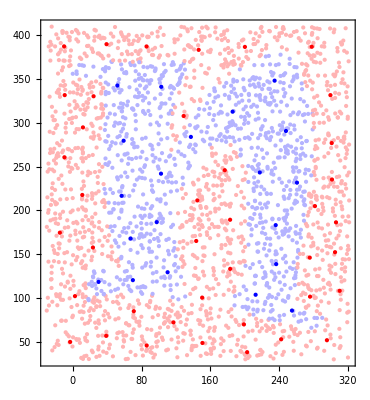

```mathematica
Show[Fig0, Graphics[{PointSize@Medium,Red, Point@centR, Blue, Point@centB}]]
```

## 3. Зоны влияния

{97.5784,186.573}

{{117.463,-43.5049},{-43.5049,211.944}}

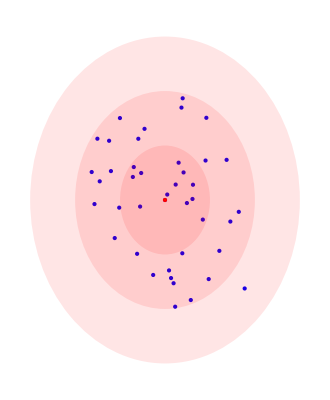

```mathematica
Mean[Train[[CB[[3]], 1;;2]]]
Covariance[Train[[CB[[3]], 1;;2]]]
Graphics[{Blue, Point@Train[[CB[[3]], 1;;2]],PointSize[Large], Point@centB⟦3⟧, Red, Point@%%,Hue[.00, 1, 1, 0.1], Ellipsoid[%%, %],Ellipsoid[%%, 4%],Ellipsoid[%%, 9%] }, PlotRange->All]
```

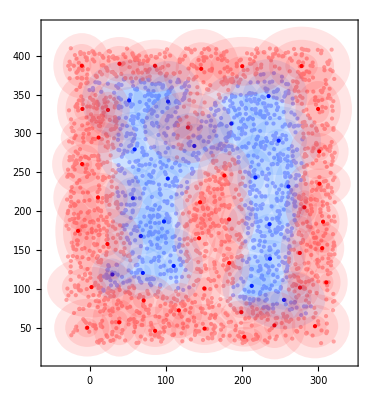

```mathematica
ClearAll[ellipse];
ellipse[l1_,l2_,q_]:=MapThread[Ellipsoid[#1,#2]&,{ConstantArray[l1⟦#⟧,3],MapThread[#1*#2&,{{1,4,9},ConstantArray[Covariance[Train⟦l2⟦#⟧,1;;2⟧],3]}]}]&/@Range[q]
Show[Fig0, Graphics[{PointSize@Medium,Red, Point@centR, Blue, Point@centB,Hue[.6, 1, 1, 0.1],ellipse[centB,CB,20],Hue[.0, 1, 1, 0.1],ellipse[centR,CR,40]},PlotRange->All]]
```

Здесь я не очень понимаю, как сделать так, чтобы центры эллипсов были ровно в центре.

## 4. Радиально - базисные функции

Матрицы ковариации для всех кластеров

```mathematica
covB=Covariance[Train⟦CB⟦#⟧,1;;2⟧]&/@Range[20];
```

```mathematica
covR=Covariance[Train⟦CR⟦#⟧,1;;2⟧]&/@Range[40];
```

Список центров всех кластеров

```mathematica
cent=Join[centB,centR];
```

Список ковариационных матриц для всех кластеров

```mathematica
cov=Join[covB,covR];
```

Функция Гаусса. На входе веторный аргумент х, размер зоны влияния (по умолчанию 3), номер кластера

```mathematica
Clear[RBF];RBF[l_,s_:3,m_Integer]:=Exp[-1/2 Inverse[(s^2)cov⟦m⟧].(l-cent⟦m⟧).(l-cent⟦m⟧)]
```

```mathematica
Manipulate[Plot3D[RBF[40*{x,y},s,u],{x,-1,10},{y,0,11},PlotRange->Full,ColorFunction->"GreenPinkTones"],{u,Range[60]},{s,1,6}]
```

## 5. Псевдообратная матрица

Функция нахождений RBF всех кластеров для строки под номером n в матрице l (s зона влияния аналогично предыдущему пункту)

```mathematica
ClearAll[func];
func[n_,l_,s_:3]:=RBF[l⟦n,1;;2⟧,s,#]&/@Range[60]
```

```mathematica
y=Train⟦All,3⟧;
```

```mathematica
M=func[#,Train]&/@Range[Length@Train];
```

```mathematica
Map[Dimensions,{U, S, V}=SingularValueDecomposition[M]]
```

{{2400,2400},{2400,60},{60,60}}

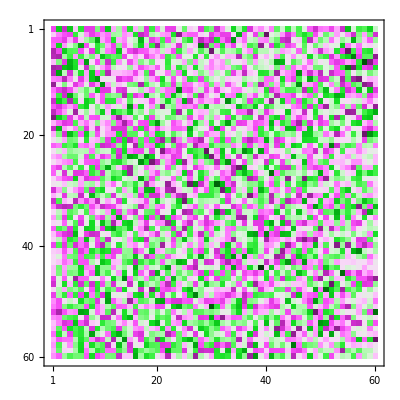

```mathematica
MatrixPlot[V,ColorFunction->"GreenPinkTones"]
```

```mathematica
MatrixPlot[U,ColorFunction->"GreenPinkTones"]
```

-Graphics-

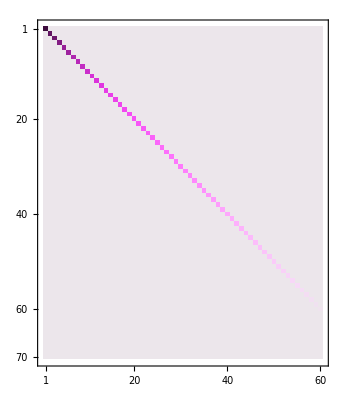

```mathematica
MatrixPlot[Take[S,70],ColorFunction->"GreenPinkTones"]
```

```mathematica
s=Diagonal[S]
```

{28.3846,23.7805,22.8535,20.3237,18.1702,17.6656,15.8864,14.983,13.8697,13.0638,11.7306,11.4526,10.6875,9.19663,8.77715,8.62517,8.1613,7.65259,7.04216,6.33298,6.16938,5.9261,5.70564,5.5646,4.7908,4.51133,4.31474,4.20861,4.08984,3.84729,3.5247,3.38717,3.209,3.1446,3.01203,2.83619,2.74665,2.72832,2.20251,2.12579,2.05781,1.87956,1.83254,1.72127,1.59544,1.54195,1.36523,1.18244,1.15373,1.07042,0.994853,0.917878,0.882133,0.814439,0.742141,0.702624,0.680166,0.590935,0.534057,0.449793}

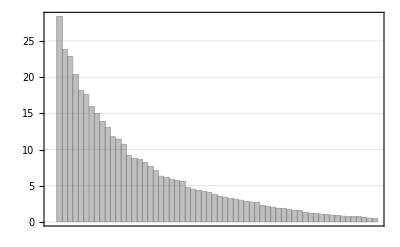

```mathematica
BarChart[%,Frame->True,GridLines->Automatic,ChartStyle->GrayLevel[0.5,0.5]]
```

```mathematica
ν=Uᵀ.y;
```

```mathematica
ξ=ν⟦1;;60⟧/s;
```

```mathematica
a=V.ξ
```

{1.06836,2.66971,-0.0312665,1.31163,0.963124,-1.93333,3.10985,2.16174,0.379312,1.66917,1.62075,0.774364,-0.59256,1.73958,2.41985,1.72052,-0.130038,1.38308,0.569056,0.893935,-1.44869,-2.45536,-0.817809,-1.2589,-0.746168,-0.041818,-1.25947,0.241998,-0.124112,-2.42585,-0.546881,-2.45098,-3.05651,-1.6155,-1.69045,-0.405266,-0.725165,-1.0795,-1.68236,0.486986,-0.56762,-0.860017,-0.0887495,-1.43679,-0.635345,-0.477487,0.933142,-0.331705,-1.52591,-0.122025,-0.0931815,-1.44379,-0.279436,-1.20009,-0.242561,-1.31806,1.57639,-0.599741,-0.229292,-0.871845}

Классификатор. На входе вектор неопределнных коэффициентов, вектор х (s аналогично)

```mathematica
ClearAll[Classifier];Classifier[a_,x_,s_:3]:=a.(RBF[x,s,#]&/@Range[60])
```

## 6. Сеть радиально - базисных функций

```mathematica
Plot3D[Classifier[a,10*{x,y}],{x,-4,32},{y,0,40},ColorFunction->"GreenPinkTones"]
```

-Graphics3D-

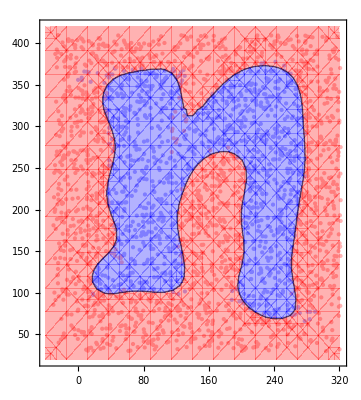

```mathematica
Show[Fig0, ContourPlot[Classifier[a,{x,y},3],{x,-40,320},{y,20,420},Contours->{0},ContourShading->{Hue[0.00,1,1,.3],Hue[0.67,1,1,0.3]},GridLines->Automatic]]
```

```mathematica
Plot3D[ UnitStep[Classifier[a,{x,y}]],{x,-40,320},{y,20,410},ColorFunction->{Hue[0.00,1,1,.8],Hue[0.67,1,1,.8]}]
```

-Graphics3D-

## 7. Ошибки первого и второго рода

Как и для тренировочного набора находим вектор неопределенных коэффициентов

```mathematica
M1=func[#,Test]&/@Range[Length@Test];
```

```mathematica
Map[Dimensions,{U1, S1, V1}=SingularValueDecomposition[M1]]
```

{{600,600},{600,60},{60,60}}

```mathematica
s1=Diagonal[S1];
```

```mathematica
y1=Test⟦All,3⟧;
```

```mathematica
ν1=U1ᵀ.y1;
```

```mathematica
ξ1=ν1⟦1;;60⟧/s1;
```

```mathematica
a1=V1.ξ1
```

{0.790204,1.61054,-1.0327,1.31517,1.08822,-2.1963,2.74147,2.55652,0.579559,2.1947,1.28901,1.41639,-0.972323,1.55439,2.98825,2.42771,0.333324,1.69569,0.321827,1.38593,-1.33209,-2.54734,-0.784968,-1.14945,-1.31611,-0.339312,-1.99262,0.91312,-0.273401,-2.59844,-0.836556,-3.25887,-3.90293,-1.77033,-1.63887,-0.413919,-0.646,-0.561049,-1.85669,1.36565,-0.443806,-0.528084,-0.344688,-1.26218,-1.0746,-0.0519578,0.848514,-0.270397,-1.60922,0.108165,-0.756901,-1.94814,-0.617061,-1.60037,0.567531,-1.223,2.26737,-1.00789,0.204865,-0.384867}

```mathematica
{a,b}=Map[Dimensions,{bl=First[#]&/@Position[Test,1.],
red=First[#]&/@Position[Test, -1.]}]
```

{{211},{389}}

```mathematica
l1=Count[UnitStep[Classifier[a1,Test⟦#,1;;2⟧]&/@bl],0]
```

19

Процент ошибок первого рода

```mathematica
N[l1/First[a]]*100
```

9.00474

```mathematica
l2=Count[UnitStep[Classifier[a1,Test⟦#,1;;2⟧]&/@red],1]
```

2

Процент ошибок второго рода

```mathematica
N[l2/First[b]]*100
```

0.514139

Полученные результаты показывают, что процент ошибок как первого, так и второго рода достаточно мал

## 8. Зависимость качества классификатора от размера зоны влияния RBF

Функция нахождения неопределенных коэффициентов для разных s

```mathematica
ClearAll[findA];findA[s_]:=Module[{M,U,V,S,ν,ξ,y}, M=func[#,Train,s]&/@Range[Length@Train];
Map[Dimensions,{U, S, V}=SingularValueDecomposition[M]];
y=Train⟦All,3⟧;
ν=Uᵀ.y;
ξ=ν⟦1;;60⟧/Diagonal[S];
V.ξ
]
```

Список из всех неопределенных коэффициентов для s = 1 ... 6

```mathematica
l=findA[#]&/@Range[6];
```

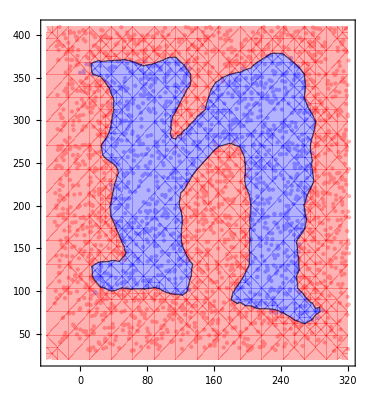
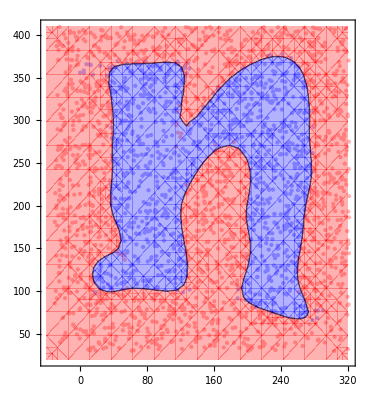
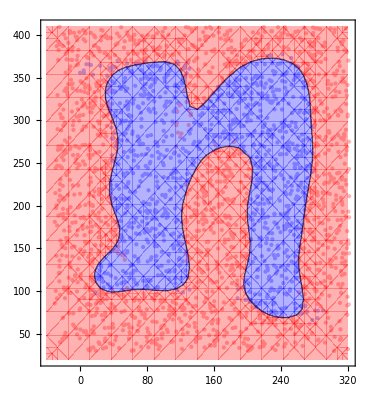
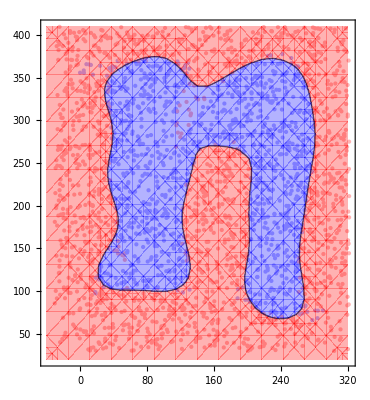
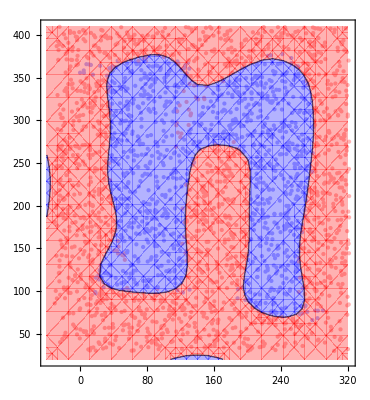
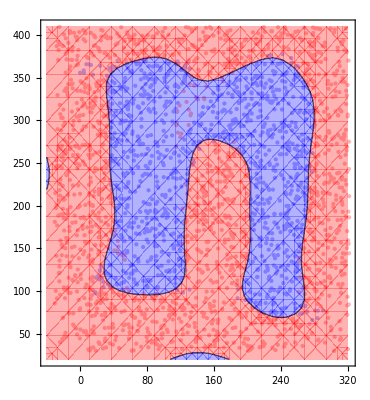
{{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-},{-Graphics3D-,-Graphics-}}

```mathematica
Table[{Plot3D[Classifier[l⟦s⟧,10*{x,y},s],{x,-4,40},{y,0,40},ColorFunction->"GreenPinkTones"],Show[Fig0, ContourPlot[Classifier[l⟦s⟧,{x,y},s],{x,-40,320},{y,20,410},Contours->{0},ContourShading->{Hue[0.00,1,1,.3],Hue[0.67,1,1,0.3]},GridLines->Automatic]]},{s,6}]
```

Зависимость качества классификатора от размера влияния RBF : чем больше зона влияние, тем хуже качество классификатора